1.

```mathematica
Norm[{2,0}]//N
Norm[{2,1}]//N
```

2.

2.23607

2.

```mathematica
colorList=Table[{Hue[i/25],Point[{i,Sin[i]}]},{i,1,25}];
```

3.

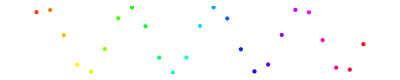

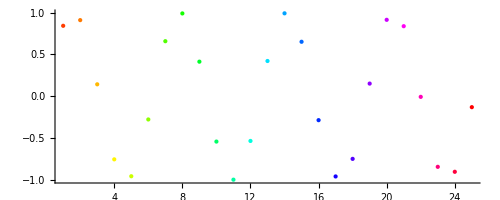

```mathematica
Graphics[colorList]
Graphics[colorList,Axes->True]
```

4.

```mathematica
a:=RandomVariate[NormalDistribution[0,1]]
b:={a,a}
```

5.

```mathematica
walk2D[n_]:= NestWhileList[b+#&,{0,0},Norm[#]≤n&]
```

6.

```mathematica
addColor[myList_]:=Table[{Hue[i/Length[myList]],Point[myList[[i]]]},{i,1,Length[myList]}]
```

7.

```mathematica
walkList=Table[walk2D[100],20];
```

8.

```mathematica
meanLength=Mean[Table[Length[walkList[[i]]],{i,1,20}]]//N
medianLength=Median[Table[Length[walkList[[i]]],{i,1,20}]]//N
```

4941.35

3614.

9.

```mathematica
Manipulate[Graphics[addColor[walkList[[i]]],Axes ->True],{i,1,20}]
```